```mathematica
Prf[l_, Pdc_,a_,b_] = l*idc^2/2 * (2*BesselJ[1,2*b])^2
```

2 idc^2 l BesselJ[1,2 b]^2

```mathematica
P3rf[l_, Pdc_,a_,b_] = l*idc^2/2 * (2*BesselJ[3,2*b])^2
```

2 idc^2 l BesselJ[3,2 b]^2

```mathematica
Plo[l_, idc_,a_,b_] = l*idc^2/2 * (2*BesselJ[1,2*a])^2
```

2 idc^2 l BesselJ[1,2 a]^2

```mathematica
Plorf[l_, idc_,a_,b_] = l*idc^2/2 * (2*BesselJ[1,2*a]*BesselJ[1,2*b])^2
```

2 idc^2 l BesselJ[1,2 a]^2 BesselJ[1,2 b]^2

```mathematica
Plo3rf[l_, idc_,a_,b_] = l*idc^2/2 * (2*BesselJ[1,2*a]*BesselJ[3,2*b])^2
```

2 idc^2 l BesselJ[1,2 a]^2 BesselJ[3,2 b]^2

```mathematica
toa[v_] = (v/4)*(Pi/2)
```

(π v)/8

```mathematica
topower[v_] = 10*Log10[v]
```

(10 Log[v])/Log[10]

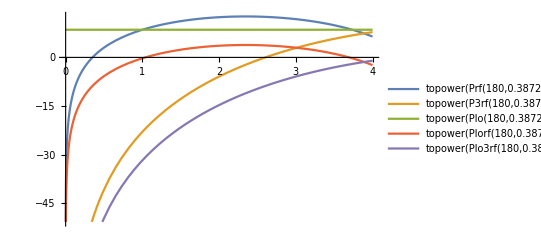

```mathematica
Plot[{topower[Prf[180,0.3872,toa[1],toa[x]]],
topower[P3rf[180,0.3872,toa[1],toa[x]]],
topower[Plo[180,0.3872,toa[1],toa[x]]],
topower[Plorf[180,0.3872,toa[1],toa[x]]],
topower[Plo3rf[180,0.3872,toa[1],toa[x]]]},{x,0,4}, PlotLegends->"Expressions"]
```